```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/c8888/IdeaProjects/ChernRetrieval

```mathematica
δx=0.5;
δy=0.5;
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
RTF=4;
rangeNeighobour= 1;
ax=1;
ay=1;
σw=0.155;
```

```mathematica
Needs["space`"]
```

```mathematica
?latticeProbingPoints
```

latticeProbingPoints[xmin, xmax, ymin, ymax, δx, δy] generates a list of points {{x_i, y_i}} at which one measures physical variables of BEC in a trap

```mathematica
lat=latticeProbingPoints[xmin,xmax,ymin,ymax,δx,δy];
```

```mathematica
lat[[1,1]]
```

-5.

```mathematica
Last[lat][[2]]
```

5.

```mathematica
?rectLatticeSites
```

rectLatticeSites[ax, ay, RTF, latticeProbingPoints, rangeNeighbour] generates two lists {l1,l2}:
    l1={{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)
    l2={{x_i_j,y_i_j}} is the list of 1..j..k points from latticeProbingPoints which are in the distance of rangeNeighbour from i_th lattice node corresponding to l1

```mathematica
rec=rectLatticeSites[ax,ay,RTF,lat,rangeNeighobour];
```

```mathematica
Dimensions@rec
```

{2,49}

```mathematica
?Sort
```

RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] sorts the elements of StyleBox["list", "TI"] into canonical order. 
RowBox[{"Sort", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["p", "TI"]}], "]"}] sorts using the ordering function StyleBox["p", "TI"].

```mathematica
recA=Map[If[#[[2]]==-1,#[[1]]]&,rec[[1]]];
```

```mathematica
recB=Map[If[#[[2]]==1,#[[1]]]&,rec[[1]]];
```

```mathematica
rec[[2,3]];
```

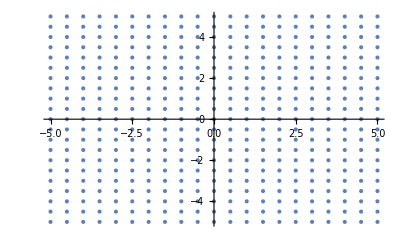

```mathematica
p1=ListPlot[lat]
```

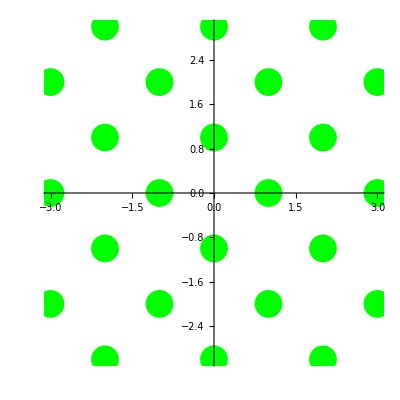

```mathematica
p2A=ListPlot[recA,PlotStyle->{PointSize->0.05,Green},AspectRatio->1]
```

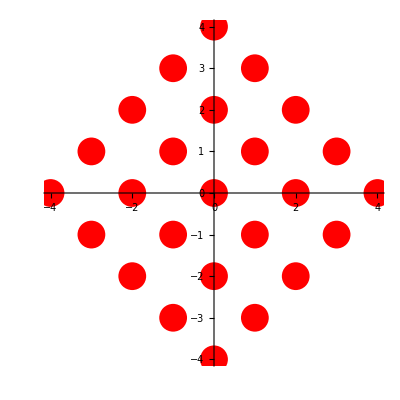

```mathematica
p2B=ListPlot[recB,PlotStyle->{PointSize->0.05,Red},AspectRatio->1]
```

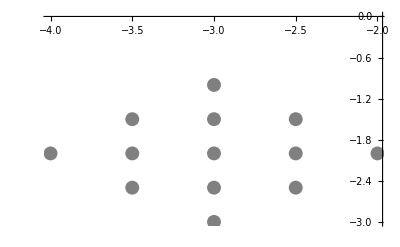

```mathematica
p3=ListPlot[rec[[2,2]],PlotStyle->{PointSize->0.025,Gray}]
```

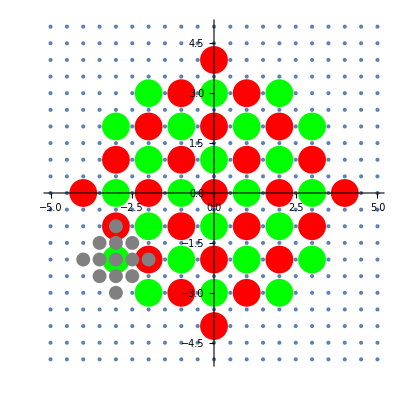

```mathematica
Show[p1,p2A,p2B,p3,AspectRatio->1]
```

```mathematica
w[r_,ri_,σw_,β_]:=β*Exp[-Norm[N[r]-N[ri]]^2/2/σw^2]
```

```mathematica
1/Sqrt[Total[Map[w[#,{0,0},0.1,1]&,lat]^2]]
```

1.

```mathematica
Chop@Map[w[#,{0,0},0.1,1]&,lat]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.72665×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.72665×10^-6,1.,3.72665×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.72665×10^-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Needs["wavefunction`"]
```

```mathematica
β=wannierNormalisationFactor[σw,δx,δy,lat]
```

1.99988

```mathematica
Plot3D[wannier[{x,y},{0,0},σw,β],{x,-2σw,2σw},{y,-2σw,2σw}]
```

-Graphics3D-